```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler2`";
STEPS=3;
CHAINS=6;
```

```mathematica
σ=1;
U[x_,y_]=1/(2 σ^2)(√(x^2+y^2)-10.)^2;
(*U[x_,y_]=(Cos[x]Cos[y]+1)4;*)
(*ρ=1-10^-15;
SIGMA={{1,ρ},{ρ,1}};
(*SIGMA={{0.6999999999999998,0.9999999999999999},{0.9999999999999999,0.6999999999999998}};*)
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
*)
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
dddU[x_,y_]=D3[U[x,y],{x,y}];
K[v_,w_,x_,y_,r_]:=Module[{Σ},
Σ=getΣ[{x,y},r,ddU];
1/2{v,w}.LinearSolve[Σ,{v,w}]];
dKdp[v_,w_,x_,y_,r_]:=Module[{Σ},
Σ=getΣ[{x,y},r,ddU];
LinearSolve[Σ,{v,w}]];
dKdq1[v_,w_,x_,y_,r_]:=Module[{g1,g0,ϵ=10^-3},
g1=(K[v,w,x+ϵ,y,r]-K[v,w,x-ϵ,y,r])/(2ϵ);
g0=(K[v,w,x,y+ϵ,r]-K[v,w,x,y-ϵ,r])/(2ϵ);
{g1,g0}];
dKdq[v0_,w_,x_,y0_,r0_]:=dKdq0[{v0,w},{x,y0},r0,ddU,dddU];
```

```mathematica
(*K[v_,w_,x_,y_,r_]:=1/2{v,w}.{v,w};
dKdp[v_,w_,x_,y_,r_]:={v,w};
dKdq[v0_,w_,x_,y0_,r0_]:=0;*)
```

```mathematica
dKdq1[1,2,3,4,1]
```

{-0.3008,0.1856}

```mathematica
dKdq[1,2,3,4,1]
```

{-0.3008,0.1856}

```mathematica
(*K[v_,w_,x_,y_,r_]:=Module[{Σ},
1/2{v,w}.{v,w}];
dKdp[v_,w_,x_,y_,r_]:=Module[{Σ},
{v,w}];
dKdq[v_,w_,x_,y_,r_]:=0;*)
```

```mathematica
INTERVAL=1001
```

1001

```mathematica
(*outbnd[q_]:=AnyTrue[q,(Abs[#]>10)&];*)
```

```mathematica
QS=hmc3[U,dU,K,dKdp,dKdq,2,5000,10000,{},levels];
```

10011.34935183047.0.7383020.4202920.8118081{1,3,4}{1,2,4}{0.6237}{1.40639}0.6237TrueFalse1

20026.6486651819.40.3332520.5162010.00674231{1,2}{2,3,4}{0.6237}{6.05037}0.6237FalseTrue1

300310.149432631.90.5749720.4621090.008870151{1,4}{1,2,3}{0.6237}{10.1583}0.6237FalseFalse1

400440.3757104774.0.4897840.536940.06609621{1,4}{1,2,3}{0.6237}{36.7212}0.6237FalseTrue1

500515.486223305.0.489860.5368910.08182591{1,2,4}{1,3}{0.6237}{15.5678}0.6237FalseTrue1

600615.4821286683.0.4893690.5365350.08567891{1,2,4}{1,3}{0.6237}{15.5678}0.6237FalseTrue1

700715.5228251351.0.326980.5046240.0449561{1,2,4}{1,3}{0.6237}{15.5678}0.6237FalseTrue1

800815.038326462.20.6582790.5090770.5294481{1,2,4}{1,3}{0.6237}{15.5678}0.6237FalseTrue1

900915.439324843.90.4864680.5336760.1284491{1,2,4}{1,3}{0.6237}{15.5678}0.6237FalseTrue1

```mathematica
(*QS=hmc2[U,dU,K,dKdp,2,5000,10000,{},levels];*)
```

```mathematica
QS1=Table[QS[[i]],{i,1,Length[QS],CHAINS}];
QS2=Table[QS[[i]],{i,2,Length[QS],CHAINS}];
QS3=Table[QS[[i]],{i,3,Length[QS],CHAINS}];
QS4=Table[QS[[i]],{i,4,Length[QS],CHAINS}];
QS5=Table[QS[[i]],{i,5,Length[QS],CHAINS}];
QS6=Table[QS[[i]],{i,6,Length[QS],CHAINS}];
Histogram[√(QS[[;;,1]]^2+QS[[;;,2]]^2),Automatic,"Probability"]
```

Balanced around 10, seems no error

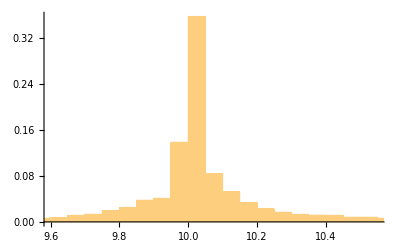

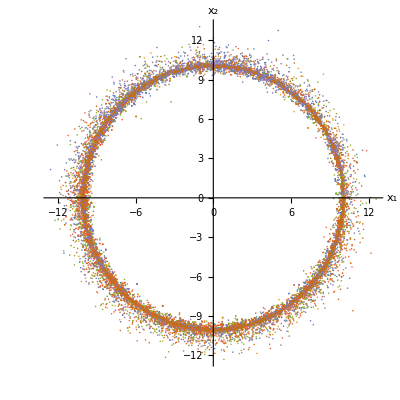

```mathematica
ListPlot[{QS1,QS2,QS3,QS4,QS5,QS6},AxesLabel->{Subscript[x, 1],Subscript[x, 2]},AspectRatio->1]
```